National Short Course in SYSTEMS BIOLOGY 
Systems Cell Biology 
Basic Chemical Reactions 
COPYRIGHT Professor Lee Bardwell, University of California, Irvine.
    This notebook requires Mathematica to run.
    Version 126 Jan 2016

```mathematica
ClearAll["Global`*"]
```

Let's start with the following ZERO ORDER CHEMICAL REACTION:
 	∅→^k A
That is, A is created from nothng at a constant rate k.  The differential equation for this reaction is: 

	A'[t] = k
	
And a reasonable initial condition is

	A[0] = 0

```mathematica
(* Use DSolve to solve the differential equation *)

DSolve[{A'[t]==k, A[0]==0}, A[t], t]
```

{{A[t]→k t}}

```mathematica
(* Use DSolve to solve the differential equation, and store the solution in a 'container'*)

ExactSolution1 =DSolve[{A'[t]==k, A[0]==0}, A[t], t]
```

{{A[t]→k t}}

```mathematica
(* Find the value of A at a single point on the time course *)

ExactSolution1/.{k->2, t-> 3}
```

{{A[3]→6}}

```mathematica
(* Another syntax that that can be used to find the value of A at a single point on the time course *)

A[t]/.ExactSolution1/.{k->2, t-> 3}
```

{6}

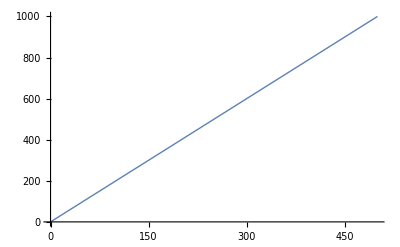

```mathematica
(* Now let's plot A[t] vs. t over the interval from 0 to 500 *)

Plot[A[t]/.ExactSolution1/.{k->2},{t,0,500}, PlotStyle->Thick]
```

Next, consider the following FIRST ORDER CHEMICAL REACTION:

	A → ∅ (or A → something)

That is, A is either destroyed, or converted to something else, and there is no reverse reation.
The differential equation for this reaction is:

	A'[t] = -k A[t]

That is, the rate at which A is disappearing at any moment in time will be proportional to amount of A at that moment

For our initial condition we will use

	A[0] = Azero

```mathematica
ClearAll["Global`*"]
ExactSolution2 =DSolve[{A'[t]==-k A[t],A[0]==Azero},A[t], t]
```

{{A[t]→Azero ⅇ^(-k t)}}

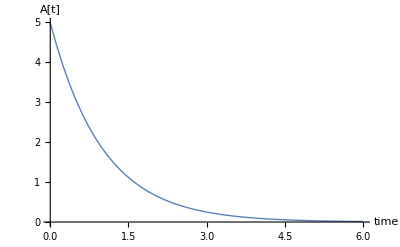

```mathematica
Plot[A[t]/.ExactSolution2/.{Azero-> 5,k->1},{t,0,6}, PlotStyle->Thick,AxesLabel-> {"time"," A[t]"}]
```

```mathematica
(* of course since we know what the exact solution is, we can use it as the input to our plot command *)

Plot[Azero ⅇ^(-k t)/.{Azero-> 5,k->1},{t,0,6}, PlotStyle->Thick,AxesLabel-> {"time"," A[t]"}]
```

-Graphics-

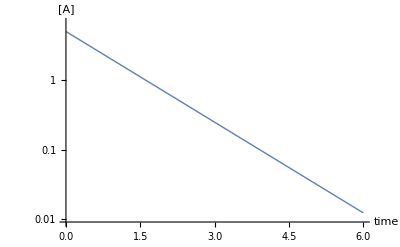

```mathematica
(* If we use a log scale to plot concentration and keep a linear scale to plot time we get straight line *)
LogPlot[A[t]/.ExactSolution2/.{Azero->5,k->1},{t,0,6}, PlotStyle->Thick,  AxesLabel->{"time","[A]"}]
```

```mathematica
(* Let's try the manupulate command with this *)
(* If there's nothing shown on the graph,choose "Evaluate Notebook" from the "Evaluation" menu *)
Manipulate[
Plot[Azero ⅇ^(-k t),{t,0,6},PlotStyle->Thick],
{k,1,10},
{Azero,1,10}]
```

```mathematica
(* Now with some more fancy options *)
Manipulate[
Plot[Azero ⅇ^(-k t),{t,0,6}, PlotRange->{0,10},AxesLabel-> {"time (s)" , "[A] (mM)"}, PlotStyle->Thick],
{{k,1},0,10,Appearance->"Labeled"},
{{Azero,10},0,10,Appearance->"Labeled"}]
```

Let's start with the following SECOND ORDER CHEMICAL REACTION:
 	A+A→^k A_2
That is, A dimerizes at a constant rate k.  The differential equation for this reaction is: 

	A'[t] = -k A[t]^2
	
There is an exact solution to this (you can find this yourself as an optional exercise).

In contrast, the SECOND ORDER CHEMICAL REACTION:
 	A+B→^k AB

Which can represent A and B binding to each other to form an AB complex, has no exact solution when modeled with the appropriate differential equations.  Rather than solve it exactly using DSolve, we must solve it numerically using NDSolve.  We'll learn more about NDSolve in a subsequent notebook.

```mathematica
(* The differential equations for the second order chemical reaction 
A + B <--> AB cannot be solved exactly, so DSolve will fail if we ask it to try  *)

ClearAll["Global`*"]
DSolve[{A'[t]==-k A[t] B[t],B'[t]==-k A[t] B[t],AB'[t]==k A[t] B[t],A[0]==Azero, B[0]==Bzero,AB[0]==0},{A[t],B[t],AB[t]}, t]
```

DSolve::bvfail: For some branches of the general solution, unable to solve the conditions.

{}

```mathematica
(* Rather than DSolve, we need to use NDSolve to get a numerical approximation *)

system ={A'[t]==-k A[t] B[t],B'[t]==-k A[t] B[t],AB'[t]==k A[t] B[t],A[0]==Azero, B[0]==Bzero,AB[0]== 0};
params = {k->1, Bzero->1.5,Azero->1};
solset1=NDSolve[system/.params,{A[t],B[t],AB[t]},{ t,0,60}]
```

{{A[t]→InterpolatingFunction[{{0., 60.}}, <>][t],B[t]→InterpolatingFunction[{{0., 60.}}, <>][t],AB[t]→InterpolatingFunction[{{0., 60.}}, <>][t]}}

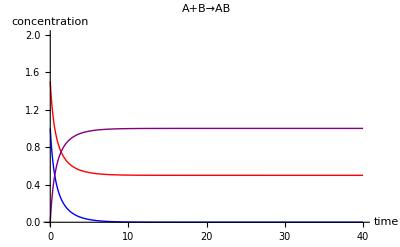

```mathematica
Plot[{A[t]/.solset1,B[t]/.solset1,AB[t]/.solset1}, {t, 0,40}, PlotRange-> {0,2},PlotStyle-> {{Blue,Thick},{Red,Thick},{Purple, Thick}},AxesLabel->{"time","concentration"}
,PlotLabel->"A+B→AB"]
```

```mathematica
(* Here I show you how to make a Manipulatable version of the interconversion reaction *)
Manipulate[
system ={A'[t]==-k A[t] B[t],B'[t]==-k A[t] B[t],AB'[t]==k A[t] B[t],A[0]==Azero, B[0]==Bzero,AB[0]== 0};
solset1=NDSolve[system/.params,{A[t],B[t],AB[t]},{ t,0,60}];
Plot[{A[t]/.solset1,B[t]/.solset1,AB[t]/.solset1}, {t, 0,40}, PlotRange-> {0,5},PlotStyle-> {{Blue,Thick},{Red,Thick},{Purple, Thick}},AxesLabel->{"time","concentration"}
,PlotLabel->"A+B→AB"],
{{Azero,3},0,10},
{{Bzero,2},0,10},
{{k,1},.1,10}
]
```